```mathematica
LX = {{.21,1/.00634296*10^-5},{.80,1/.00366724*10^-5},{1.5,1/.00138689*10^-5}};
LY  = {{.21,1/.0252088*10^-5},{.80,1/.0272929*10^-5},{1.5,1/.0164848*10^-5}};
CX = {{.12,1/.035892*10^-5},{.51,1/.0278502*10^-5},{1.00,1/.0159368*10^-5}};
CY = {{.12,1/.0371539*10^-5},{.51,1/.0272929*10^-5},{1.00,1/.0164848*10^-5}};
```

```mathematica
FLX = NonlinearModelFit[LX,w*Sqrt[(1+(z/z0)^2)],{w,z0},z]
FLY = NonlinearModelFit[LY,w*Sqrt[(1+(z/z0)^2)],{w,z0},z]
FCX = NonlinearModelFit[CX,w*Sqrt[(1+(z/z0)^2)],{w,z0},z]
 FCY= NonlinearModelFit[CY,w*Sqrt[(1+(z/z0)^2)],{w,z0},z]
```

FittedModel[0.000940721 √(1+22.3605 z^2)]

FittedModel[0.000351836 √(1+0.776577 z^2)]

FittedModel[0.000256722 √(1+4.78155 z^2)]

FittedModel[0.00025509 √(1+4.57343 z^2)]

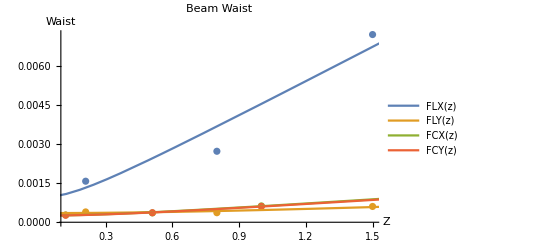

```mathematica
Show[ListPlot[{LX,LY,CX,CY},PlotLabel->"Beam Waist",AxesLabel->{Z ,Waist},PlotRange->All],Plot[{FLX[z],FLY[z],FCX[z],FCY[z]},{z,0,200},PlotLegends->"Expressions"]]
```

```mathematica
Subscript[w, 0] = 0.000940721182987842;
```

```mathematica
z0 = π*Subscript[w, 0]^2/(1228*10^-9);
z0 =22.36045953689289 
R[z_] := z*(1+(z0/z)^2)
```

22.3605

```mathematica
w[z_ ] := Subscript[w, 0]*Sqrt[1+(z/z0)^2]
```

```mathematica
(* Assume fiber coupler is at z = 100 cm, then we want 1/q = -i λ/πnw, where w is the Subscript[w, 0] of the fiber output beam. We can calculate the q of the laser output at z = 15 cm where it exits the laser box to be*)
```

```mathematica
Subscript[q, inv (laser)]=1/R[.15]-ⅈ*(1228*10^-9)/(π*w[.15])
Subscript[q, inv (fiber)]=-ⅈ*(1228*10^-9)/(π*0.0002567215675802117)
```

0.000299992-0.000415506 ⅈ

0.-0.0015226 ⅈ

```mathematica
(*Next I assume 100 cm of path length for optics, then calculate a T matrix for two cylindrical lenses, where the second lens is placed at an unknown distance L*)
```

```mathematica
Subscript[f, 1] = 250*10^-3;
Subscript[f, 2] = 100 *10^-3;
T  = ({{1, 1-L}, {0, 1}}).({{1, 0}, {-1/Subscript[f, 2], 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-1/Subscript[f, 1], 1}})
T  = ({{1, 1-L}, {0, 1}}).({{1, 0}, {-1/Subscript[f, 2], 1}}).({{1, L}, {0, 1}}).({{1, 0}, {-1/Subscript[f, 1], 1}}) //MatrixForm
```

{{1-10 (1-L)-4 (1-L+(1-10 (1-L)) L),1-L+(1-10 (1-L)) L},{-10-4 (1-10 L),1-10 L}}

(1-10 (1-L)-4 (1-L+(1-10 (1-L)) L) | 1-L+(1-10 (1-L)) L
-10-4 (1-10 L) | 1-10 L)

```mathematica
a[L_] :=1-10 (1-L)-4 (1-L+(1-10 (1-L)) L);
b[L_] :=1-L+(1-10 (1-L)) L;
c [L_]:=-10-4 (1-10 L);
d [L_]:= 1-10 L;
```

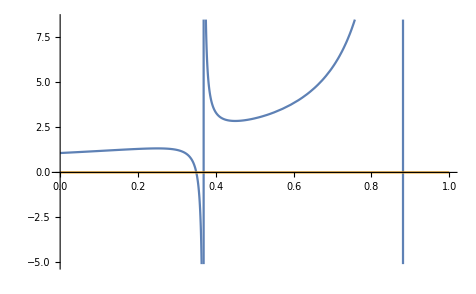

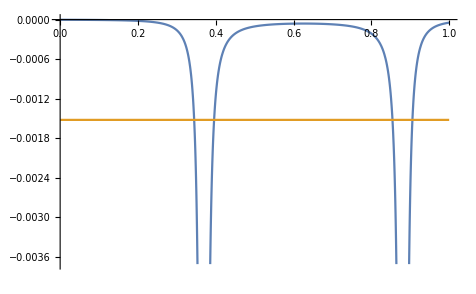

```mathematica
(* Now we can solve for the propogated q parameter with the formula 1/Subscript[q, 2] = (C+D(1/Subscript[q, 1]))/(A+B(1/Subscript[q, 1])) *)
Subscript[q2, inv (laser)][L_] := (c[L]+d[L]*Subscript[q, inv (laser)])/(a[L]+b[L]*Subscript[q, inv (laser)])
Plot[{Re[Subscript[q2, inv (laser)][L]],y=0},{L,0,1}] 

Plot[{Im[Subscript[q2, inv (laser)][L]],y=Im[Subscript[q, inv (fiber)]]},{L,0,1}]
```

```mathematica
Re[Subscript[q2, inv (laser)][.35]]
Im[Subscript[q2, inv (laser)][.35]]
```

0.00187659

-0.00259195

```mathematica
Subscript[f,1]=400*10^-3;
Subscript[f,2]=100*10^-3;
T=({{1,1-L},{0,1}}).({{1,0},{-1/Subscript[f,2],1}}).({{1,L},{0,1}}).({{1,0},{-1/Subscript[f,1],1}})
T=({{1,1-L},{0,1}}).({{1,0},{-1/Subscript[f,2],1}}).({{1,L},{0,1}}).({{1,0},{-1/Subscript[f,1],1}})//MatrixForm
```

{{1-10 (1-L)-5/2 (1-L+(1-10 (1-L)) L),1-L+(1-10 (1-L)) L},{-10-5/2 (1-10 L),1-10 L}}

(1-10 (1-L)-5/2 (1-L+(1-10 (1-L)) L) | 1-L+(1-10 (1-L)) L
-10-5/2 (1-10 L) | 1-10 L)

```mathematica
a[L_] := 1-10 (1-L)-5/2 (1-L+(1-10 (1-L)) L);
b[L_] := 1-L+(1-10 (1-L)) L;
c [L_]:= -10-5/2 (1-10 L);
d [L_]:= 1-10 L;
```

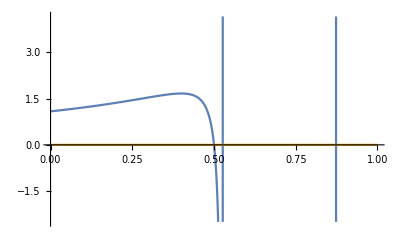

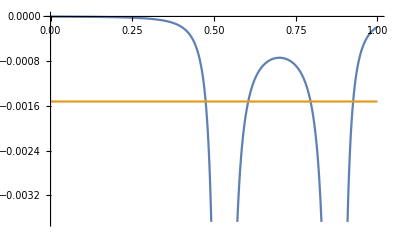

```mathematica
Subscript[q2, inv (laser)][L_] := (c[L]+d[L]*Subscript[q, inv (laser)])/(a[L]+b[L]*Subscript[q, inv (laser)])
Plot[{Re[Subscript[q2, inv (laser)][L]],y=0},{L,0,1}] 
Plot[{Im[Subscript[q2, inv (laser)][L]],y=Im[Subscript[q, inv (fiber)]]},{L,0,1}]
```

```mathematica
Re[Subscript[q2, inv (laser)][.5]]
Im[Subscript[q2, inv (laser)][.5]]
```